```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[27],OddQ]
nFaulhaber[2,5]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

55

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Algebraic Number Theory

Introduction

A crash course in Ring Theory

## Basic Definitions

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Ideals, Homomorphisms, and Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Principal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Operations on Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime and Maximal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Lattices

## Group Structure of Lattices

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Linear Algebra over ℤ

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Computing with Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Lattice Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Arithmetic in Q[d]

## Quadratic Fields

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ring of Integers

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals: The Roadmap

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Noether Rings

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Standard Form of an Ideal

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ideal Norm

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Fractional Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime Ideals in O

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

The Ideal Class Group and the Geometry of Numbers

Continued Fractions

Quadratic Forms

Notes

## tmp-1

```mathematica
Needs["AbstractAlgebra`Master`"]
```

```mathematica
SwitchStructureTo[Ring];
```

```mathematica
R1=Z[5,I,Structure->Ring]
CayleyTables[R1,Mode->Visual]
```

Ringoid[{0,ⅈ,2 ⅈ,3 ⅈ,4 ⅈ,1,1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,2,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,3,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,4,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ},-Addition-,-Multiplication-]

+ | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g1 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g2 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21
g3 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22
g4 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23
g5 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24
g6 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5
g7 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1
g8 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2
g9 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3
g10 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4
g11 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10
g12 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6
g13 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7
g14 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8
g15 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9
g16 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15
g17 | g17 | g18 | g19 | g20 | g16 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11
g18 | g18 | g19 | g20 | g16 | g17 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12
g19 | g19 | g20 | g16 | g17 | g18 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13
g20 | g20 | g16 | g17 | g18 | g19 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14
g21 | g21 | g22 | g23 | g24 | g25 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20
g22 | g22 | g23 | g24 | g25 | g21 | g2 | g3 | g4 | g5 | g1 | g7 | g8 | g9 | g10 | g6 | g12 | g13 | g14 | g15 | g11 | g17 | g18 | g19 | g20 | g16
g23 | g23 | g24 | g25 | g21 | g22 | g3 | g4 | g5 | g1 | g2 | g8 | g9 | g10 | g6 | g7 | g13 | g14 | g15 | g11 | g12 | g18 | g19 | g20 | g16 | g17
g24 | g24 | g25 | g21 | g22 | g23 | g4 | g5 | g1 | g2 | g3 | g9 | g10 | g6 | g7 | g8 | g14 | g15 | g11 | g12 | g13 | g19 | g20 | g16 | g17 | g18
g25 | g25 | g21 | g22 | g23 | g24 | g5 | g1 | g2 | g3 | g4 | g10 | g6 | g7 | g8 | g9 | g15 | g11 | g12 | g13 | g14 | g20 | g16 | g17 | g18 | g19  Add.KEY for Add(Z[5, I]): label used → element: {g1→0,g2→ⅈ,g3→2 ⅈ,g4→3 ⅈ,g5→4 ⅈ,g6→1,g7→1+ⅈ,g8→1+2 ⅈ,g9→1+3 ⅈ,g10→1+4 ⅈ,g11→2,g12→2+ⅈ,g13→2+2 ⅈ,g14→2+3 ⅈ,g15→2+4 ⅈ,g16→3,g17→3+ⅈ,g18→3+2 ⅈ,g19→3+3 ⅈ,g20→3+4 ⅈ,g21→4,g22→4+ⅈ,g23→4+2 ⅈ,g24→4+3 ⅈ,g25→4+4 ⅈ}* | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1
g2 | g1 | g21 | g16 | g11 | g6 | g2 | g22 | g17 | g12 | g7 | g3 | g23 | g18 | g13 | g8 | g4 | g24 | g19 | g14 | g9 | g5 | g25 | g20 | g15 | g10
g3 | g1 | g16 | g6 | g21 | g11 | g3 | g18 | g8 | g23 | g13 | g5 | g20 | g10 | g25 | g15 | g2 | g17 | g7 | g22 | g12 | g4 | g19 | g9 | g24 | g14
g4 | g1 | g11 | g21 | g6 | g16 | g4 | g14 | g24 | g9 | g19 | g2 | g12 | g22 | g7 | g17 | g5 | g15 | g25 | g10 | g20 | g3 | g13 | g23 | g8 | g18
g5 | g1 | g6 | g11 | g16 | g21 | g5 | g10 | g15 | g20 | g25 | g4 | g9 | g14 | g19 | g24 | g3 | g8 | g13 | g18 | g23 | g2 | g7 | g12 | g17 | g22
g6 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g17 | g18 | g19 | g20 | g21 | g22 | g23 | g24 | g25
g7 | g1 | g22 | g18 | g14 | g10 | g7 | g3 | g24 | g20 | g11 | g13 | g9 | g5 | g21 | g17 | g19 | g15 | g6 | g2 | g23 | g25 | g16 | g12 | g8 | g4
g8 | g1 | g17 | g8 | g24 | g15 | g8 | g24 | g15 | g1 | g17 | g15 | g1 | g17 | g8 | g24 | g17 | g8 | g24 | g15 | g1 | g24 | g15 | g1 | g17 | g8
g9 | g1 | g12 | g23 | g9 | g20 | g9 | g20 | g1 | g12 | g23 | g12 | g23 | g9 | g20 | g1 | g20 | g1 | g12 | g23 | g9 | g23 | g9 | g20 | g1 | g12
g10 | g1 | g7 | g13 | g19 | g25 | g10 | g11 | g17 | g23 | g4 | g14 | g20 | g21 | g2 | g8 | g18 | g24 | g5 | g6 | g12 | g22 | g3 | g9 | g15 | g16
g11 | g1 | g3 | g5 | g2 | g4 | g11 | g13 | g15 | g12 | g14 | g21 | g23 | g25 | g22 | g24 | g6 | g8 | g10 | g7 | g9 | g16 | g18 | g20 | g17 | g19
g12 | g1 | g23 | g20 | g12 | g9 | g12 | g9 | g1 | g23 | g20 | g23 | g20 | g12 | g9 | g1 | g9 | g1 | g23 | g20 | g12 | g20 | g12 | g9 | g1 | g23
g13 | g1 | g18 | g10 | g22 | g14 | g13 | g5 | g17 | g9 | g21 | g25 | g12 | g4 | g16 | g8 | g7 | g24 | g11 | g3 | g20 | g19 | g6 | g23 | g15 | g2
g14 | g1 | g13 | g25 | g7 | g19 | g14 | g21 | g8 | g20 | g2 | g22 | g9 | g16 | g3 | g15 | g10 | g17 | g4 | g11 | g23 | g18 | g5 | g12 | g24 | g6
g15 | g1 | g8 | g15 | g17 | g24 | g15 | g17 | g24 | g1 | g8 | g24 | g1 | g8 | g15 | g17 | g8 | g15 | g17 | g24 | g1 | g17 | g24 | g1 | g8 | g15
g16 | g1 | g4 | g2 | g5 | g3 | g16 | g19 | g17 | g20 | g18 | g6 | g9 | g7 | g10 | g8 | g21 | g24 | g22 | g25 | g23 | g11 | g14 | g12 | g15 | g13
g17 | g1 | g24 | g17 | g15 | g8 | g17 | g15 | g8 | g1 | g24 | g8 | g1 | g24 | g17 | g15 | g24 | g17 | g15 | g8 | g1 | g15 | g8 | g1 | g24 | g17
g18 | g1 | g19 | g7 | g25 | g13 | g18 | g6 | g24 | g12 | g5 | g10 | g23 | g11 | g4 | g17 | g22 | g15 | g3 | g16 | g9 | g14 | g2 | g20 | g8 | g21
g19 | g1 | g14 | g22 | g10 | g18 | g19 | g2 | g15 | g23 | g6 | g7 | g20 | g3 | g11 | g24 | g25 | g8 | g16 | g4 | g12 | g13 | g21 | g9 | g17 | g5
g20 | g1 | g9 | g12 | g20 | g23 | g20 | g23 | g1 | g9 | g12 | g9 | g12 | g20 | g23 | g1 | g23 | g1 | g9 | g12 | g20 | g12 | g20 | g23 | g1 | g9
g21 | g1 | g5 | g4 | g3 | g2 | g21 | g25 | g24 | g23 | g22 | g16 | g20 | g19 | g18 | g17 | g11 | g15 | g14 | g13 | g12 | g6 | g10 | g9 | g8 | g7
g22 | g1 | g25 | g19 | g13 | g7 | g22 | g16 | g15 | g9 | g3 | g18 | g12 | g6 | g5 | g24 | g14 | g8 | g2 | g21 | g20 | g10 | g4 | g23 | g17 | g11
g23 | g1 | g20 | g9 | g23 | g12 | g23 | g12 | g1 | g20 | g9 | g20 | g9 | g23 | g12 | g1 | g12 | g1 | g20 | g9 | g23 | g9 | g23 | g12 | g1 | g20
g24 | g1 | g15 | g24 | g8 | g17 | g24 | g8 | g17 | g1 | g15 | g17 | g1 | g15 | g24 | g8 | g15 | g24 | g8 | g17 | g1 | g8 | g17 | g1 | g15 | g24
g25 | g1 | g10 | g14 | g18 | g22 | g25 | g4 | g8 | g12 | g16 | g19 | g23 | g2 | g6 | g15 | g13 | g17 | g21 | g5 | g9 | g7 | g11 | g20 | g24 | g3  Mult.

```mathematica
R2=Z[20,5]
CayleyTables[R2,Mode->Visual]
```

Ringoid[{0,5,10,15},Mod[#1+#2,20]&,Mod[#1 #2,20]&]

+ | 0 | 5 | 10 | 15
0 | 0 | 5 | 10 | 15
5 | 5 | 10 | 15 | 0
10 | 10 | 15 | 0 | 5
15 | 15 | 0 | 5 | 10  Add.* | 0 | 5 | 10 | 15
0 | 0 | 0 | 0 | 0
5 | 0 | 5 | 10 | 15
10 | 0 | 10 | 0 | 10
15 | 0 | 15 | 10 | 5  Mult.

```mathematica
RingQ[R2]
FieldQ[R2]
Units[R2]
```

True

False

{5,15}

```mathematica
FieldQ[Z[30,6]]
```

True

```mathematica
M=Mat[Z[2],{2,2}]
```

-Mat_2(Z[2])-

```mathematica
Map[#//mf&,Domain[M]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

```mathematica
R3=ToRingoid[Mat[Z[2],2]]
```

Ringoid[{{{0,0},{0,0}},{{0,0},{0,1}},{{0,0},{1,0}},{{0,0},{1,1}},{{0,1},{0,0}},{{0,1},{0,1}},{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{0,0}},{{1,0},{0,1}},{{1,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,0}},{{1,1},{0,1}},{{1,1},{1,0}},{{1,1},{1,1}}},-Addition-,-Multiplication-]

```mathematica
RingQ[R3]
```

True

```mathematica
CayleyTables[R3,Mode->Visual]
```

+ | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g2 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15
g3 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14
g4 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13
g5 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12
g6 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11
g7 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10
g8 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9
g9 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8
g10 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7
g11 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6
g12 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5
g13 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4
g14 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3
g15 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2
g16 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1  Add.KEY for Add(-Mat   (Z[2])-)
        (2): label used → element: …* | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1
g2 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4
g3 | g1 | g1 | g1 | g1 | g2 | g2 | g2 | g2 | g3 | g3 | g3 | g3 | g4 | g4 | g4 | g4
g4 | g1 | g2 | g3 | g4 | g2 | g1 | g4 | g3 | g3 | g4 | g1 | g2 | g4 | g3 | g2 | g1
g5 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13
g6 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16
g7 | g1 | g5 | g9 | g13 | g2 | g6 | g10 | g14 | g3 | g7 | g11 | g15 | g4 | g8 | g12 | g16
g8 | g1 | g6 | g11 | g16 | g2 | g5 | g12 | g15 | g3 | g8 | g9 | g14 | g4 | g7 | g10 | g13
g9 | g1 | g1 | g1 | g1 | g5 | g5 | g5 | g5 | g9 | g9 | g9 | g9 | g13 | g13 | g13 | g13
g10 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g11 | g1 | g1 | g1 | g1 | g6 | g6 | g6 | g6 | g11 | g11 | g11 | g11 | g16 | g16 | g16 | g16
g12 | g1 | g2 | g3 | g4 | g6 | g5 | g8 | g7 | g11 | g12 | g9 | g10 | g16 | g15 | g14 | g13
g13 | g1 | g5 | g9 | g13 | g5 | g1 | g13 | g9 | g9 | g13 | g1 | g5 | g13 | g9 | g5 | g1
g14 | g1 | g6 | g11 | g16 | g5 | g2 | g15 | g12 | g9 | g14 | g3 | g8 | g13 | g10 | g7 | g4
g15 | g1 | g5 | g9 | g13 | g6 | g2 | g14 | g10 | g11 | g15 | g3 | g7 | g16 | g12 | g8 | g4
g16 | g1 | g6 | g11 | g16 | g6 | g1 | g16 | g11 | g11 | g16 | g1 | g6 | g16 | g11 | g6 | g1  Mult.

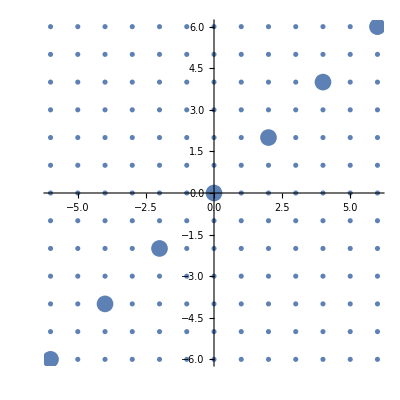

```mathematica
gr=IntegerLatticeGrid[{-6,6},{-6,6},AspectRatio->Automatic];
z=2+2I;
someMultipliers=Table[k,{k,-3,3}];
idealList = someMultipliers * z;
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

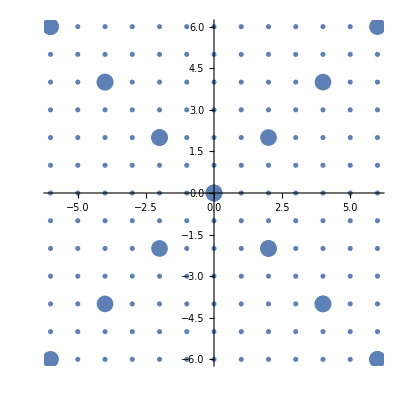

```mathematica
addToIdealList=Table[k I,{k,-3,3}] z;
idealList=Join[idealList,addToIdealList];
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},AspectRatio->Automatic,DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

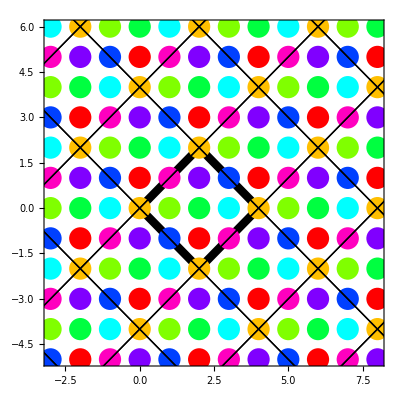

```mathematica
QuotientRing[Z[I],2+2I,Mode->Visual,Form->Representatives]
```

```mathematica
QuotientRing[Z[I],2+2I]
```

Ringoid[{J,1+J,2+J,3+J,(3+ⅈ)+J,(2+ⅈ)+J,(1+ⅈ)+J,(2-ⅈ)+J},-Addition-,-Multiplication-]

```mathematica
R=Z[45];
B1={0,15,30};
B2={0,9,18,27,36};
IdealQ[B1,R]
IdealQ[B2,R]
CayleyTables[QuotientRing[R,B2],Mode->Visual]
```

True

True

+ | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
1+NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS
2+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS
3+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS
4+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS
5+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS
6+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS
7+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS
8+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS  Add.* | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | NS | NS | NS | NS | NS | NS | NS | NS
1+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
2+NS | NS | 2+NS | 4+NS | 6+NS | 8+NS | 1+NS | 3+NS | 5+NS | 7+NS
3+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS
4+NS | NS | 4+NS | 8+NS | 3+NS | 7+NS | 2+NS | 6+NS | 1+NS | 5+NS
5+NS | NS | 5+NS | 1+NS | 6+NS | 2+NS | 7+NS | 3+NS | 8+NS | 4+NS
6+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS
7+NS | NS | 7+NS | 5+NS | 3+NS | 1+NS | 8+NS | 6+NS | 4+NS | 2+NS
8+NS | NS | 8+NS | 7+NS | 6+NS | 5+NS | 4+NS | 3+NS | 2+NS | 1+NS  Mult.

## AddTwo via WSTP

```mathematica
SetDirectory["C:/Users/Nilo/__DATA/Mega/DATA/MyTexifyProjects/FreitagBusamExercises/src/Mathematica/WSTP"]
```

C:\Users\Nilo\__DATA\Mega\DATA\MyTexifyProjects\FreitagBusamExercises\src\Mathematica\WSTP

```mathematica
link = Install["./addtwo"]
```

LinkObject[…]

```mathematica
?AddTwo
```

```mathematica
AddTwo[1,3]
```

4

```mathematica
Uninstall[link]
```

./addtwo

## Overzetten naar NotesMMa

```mathematica
{1,21,3,4,1,2}/. 1:>10
```

{10,21,3,4,10,2}

```mathematica
$CloudCreditsAvailable
```

105000

```mathematica
FullForm[(3/2+1/2I)/(1/2)]
(3/2+1/2I)/(1/2)
Complex[1,1]
?Complex
```

Complex[3,1]

3+ⅈ

1+ⅈ

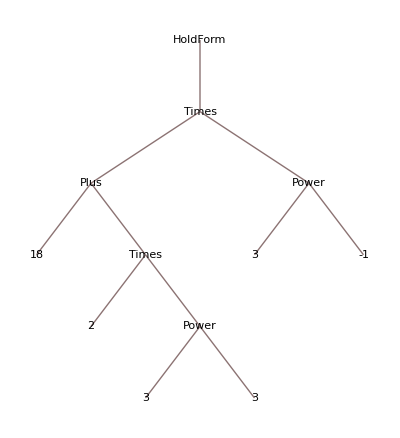

```mathematica
TreeForm[HoldForm[(18+2 3^3)/3]]
```

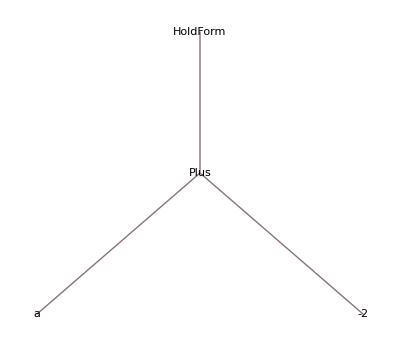

```mathematica
HoldForm[a-2] //TreeForm
```

```mathematica
x:=2
Clear[f]
f[x_,y_]:=x+y
f[3,√2]
f[2,3]
```

3+√2

5

```mathematica
x:=2
Clear[f]
f[x_,y_]=x+y
f[3,√2]
f[2,3]
```

2+y

2+√2

5

```mathematica
Array[Prime,1229]/. (x_:> {x,NumberFieldClassNumber[Sqrt[x]]})//Transpose//tf
```

2 | 1
3 | 1
5 | 1
7 | 1
11 | 1
13 | 1
17 | 1
19 | 1
23 | 1
29 | 1
31 | 1
37 | 1
41 | 1
43 | 1
47 | 1
53 | 1
59 | 1
61 | 1
67 | 1
71 | 1
73 | 1
79 | 3
83 | 1
89 | 1
97 | 1
101 | 1
103 | 1
107 | 1
109 | 1
113 | 1
127 | 1
131 | 1
137 | 1
139 | 1
149 | 1
151 | 1
157 | 1
163 | 1
167 | 1
173 | 1
179 | 1
181 | 1
191 | 1
193 | 1
197 | 1
199 | 1
211 | 1
223 | 3
227 | 1
229 | 3
233 | 1
239 | 1
241 | 1
251 | 1
257 | 3
263 | 1
269 | 1
271 | 1
277 | 1
281 | 1
283 | 1
293 | 1
307 | 1
311 | 1
313 | 1
317 | 1
331 | 1
337 | 1
347 | 1
349 | 1
353 | 1
359 | 3
367 | 1
373 | 1
379 | 1
383 | 1
389 | 1
397 | 1
401 | 5
409 | 1
419 | 1
421 | 1
431 | 1
433 | 1
439 | 5
443 | 3
449 | 1
457 | 1
461 | 1
463 | 1
467 | 1
479 | 1
487 | 1
491 | 1
499 | 5
503 | 1
509 | 1
521 | 1
523 | 1
541 | 1
547 | 1
557 | 1
563 | 1
569 | 1
571 | 1
577 | 7
587 | 1
593 | 1
599 | 1
601 | 1
607 | 1
613 | 1
617 | 1
619 | 1
631 | 1
641 | 1
643 | 1
647 | 1
653 | 1
659 | 3
661 | 1
673 | 1
677 | 1
683 | 1
691 | 1
701 | 1
709 | 1
719 | 1
727 | 5
733 | 3
739 | 1
743 | 1
751 | 1
757 | 1
761 | 3
769 | 1
773 | 1
787 | 1
797 | 1
809 | 1
811 | 1
821 | 1
823 | 1
827 | 1
829 | 1
839 | 3
853 | 1
857 | 1
859 | 1
863 | 1
877 | 1
881 | 1
883 | 1
887 | 1
907 | 1
911 | 1
919 | 1
929 | 1
937 | 1
941 | 1
947 | 1
953 | 1
967 | 1
971 | 1
977 | 1
983 | 1
991 | 1
997 | 1
1009 | 7
1013 | 1
1019 | 1
1021 | 1
1031 | 1
1033 | 1
1039 | 1
1049 | 1
1051 | 1
1061 | 1
1063 | 1
1069 | 1
1087 | 7
1091 | 3
1093 | 5
1097 | 1
1103 | 1
1109 | 1
1117 | 1
1123 | 1
1129 | 9
1151 | 1
1153 | 1
1163 | 1
1171 | 3
1181 | 1
1187 | 1
1193 | 1
1201 | 1
1213 | 1
1217 | 1
1223 | 3
1229 | 3
1231 | 1
1237 | 1
1249 | 1
1259 | 1
1277 | 1
1279 | 1
1283 | 1
1289 | 1
1291 | 1
1297 | 11
1301 | 1
1303 | 1
1307 | 1
1319 | 1
1321 | 1
1327 | 5
1361 | 1
1367 | 3
1373 | 3
1381 | 1
1399 | 1
1409 | 1
1423 | 1
1427 | 1
1429 | 5
1433 | 1
1439 | 1
1447 | 1
1451 | 1
1453 | 1
1459 | 1
1471 | 1
1481 | 1
1483 | 1
1487 | 1
1489 | 3
1493 | 1
1499 | 1
1511 | 1
1523 | 3
1531 | 1
1543 | 1
1549 | 1
1553 | 1
1559 | 1
1567 | 3
1571 | 1
1579 | 1
1583 | 1
1597 | 1
1601 | 7
1607 | 1
1609 | 1
1613 | 1
1619 | 1
1621 | 1
1627 | 3
1637 | 1
1657 | 1
1663 | 1
1667 | 1
1669 | 1
1693 | 1
1697 | 1
1699 | 1
1709 | 1
1721 | 1
1723 | 1
1733 | 1
1741 | 1
1747 | 1
1753 | 1
1759 | 1
1777 | 1
1783 | 1
1787 | 3
1789 | 1
1801 | 1
1811 | 3
1823 | 1
1831 | 1
1847 | 3
1861 | 1
1867 | 1
1871 | 1
1873 | 1
1877 | 1
1879 | 1
1889 | 1
1901 | 3
1907 | 3
1913 | 1
1931 | 1
1933 | 1
1949 | 1
1951 | 1
1973 | 1
1979 | 1
1987 | 3
1993 | 1
1997 | 1
1999 | 1
2003 | 1
2011 | 1
2017 | 1
2027 | 5
2029 | 7
2039 | 1
2053 | 1
2063 | 1
2069 | 1
2081 | 5
2083 | 1
2087 | 1
2089 | 3
2099 | 3
2111 | 1
2113 | 1
2129 | 1
2131 | 1
2137 | 1
2141 | 1
2143 | 3
2153 | 5
2161 | 1
2179 | 1
2203 | 1
2207 | 3
2213 | 3
2221 | 1
2237 | 1
2239 | 1
2243 | 1
2251 | 7
2267 | 1
2269 | 1
2273 | 1
2281 | 1
2287 | 1
2293 | 1
2297 | 1
2309 | 1
2311 | 1
2333 | 1
2339 | 1
2341 | 1
2347 | 1
2351 | 1
2357 | 1
2371 | 1
2377 | 1
2381 | 1
2383 | 1
2389 | 1
2393 | 1
2399 | 5
2411 | 1
2417 | 1
2423 | 1
2437 | 1
2441 | 1
2447 | 1
2459 | 3
2467 | 7
2473 | 1
2477 | 1
2503 | 1
2521 | 1
2531 | 1
2539 | 1
2543 | 3
2549 | 1
2551 | 1
2557 | 3
2579 | 1
2591 | 1
2593 | 1
2609 | 1
2617 | 1
2621 | 1
2633 | 1
2647 | 1
2657 | 1
2659 | 3
2663 | 1
2671 | 1
2677 | 3
2683 | 1
2687 | 1
2689 | 1
2693 | 1
2699 | 1
2707 | 1
2711 | 3
2713 | 3
2719 | 1
2729 | 1
2731 | 1
2741 | 1
2749 | 1
2753 | 1
2767 | 1
2777 | 3
2789 | 1
2791 | 1
2797 | 1
2801 | 1
2803 | 1
2819 | 1
2833 | 1
2837 | 1
2843 | 1
2851 | 1
2857 | 3
2861 | 1
2879 | 1
2887 | 1
2897 | 1
2903 | 1
2909 | 1
2917 | 3
2927 | 1
2939 | 1
2953 | 1
2957 | 1
2963 | 1
2969 | 1
2971 | 3
2999 | 1
3001 | 1
3011 | 1
3019 | 1
3023 | 3
3037 | 1
3041 | 1
3049 | 1
3061 | 1
3067 | 1
3079 | 1
3083 | 1
3089 | 1
3109 | 1
3119 | 1
3121 | 5
3137 | 9
3163 | 3
3167 | 1
3169 | 1
3181 | 5
3187 | 1
3191 | 1
3203 | 1
3209 | 1
3217 | 1
3221 | 3
3229 | 3
3251 | 5
3253 | 5
3257 | 1
3259 | 1
3271 | 1
3299 | 1
3301 | 1
3307 | 1
3313 | 1
3319 | 1
3323 | 1
3329 | 1
3331 | 1
3343 | 1
3347 | 1
3359 | 1
3361 | 1
3371 | 1
3373 | 1
3389 | 1
3391 | 3
3407 | 1
3413 | 1
3433 | 1
3449 | 1
3457 | 1
3461 | 1
3463 | 1
3467 | 1
3469 | 1
3491 | 1
3499 | 1
3511 | 1
3517 | 1
3527 | 1
3529 | 1
3533 | 1
3539 | 1
3541 | 1
3547 | 1
3557 | 1
3559 | 1
3571 | 1
3581 | 1
3583 | 1
3593 | 1
3607 | 1
3613 | 1
3617 | 1
3623 | 1
3631 | 1
3637 | 1
3643 | 1
3659 | 1
3671 | 1
3673 | 1
3677 | 1
3691 | 1
3697 | 1
3701 | 1
3709 | 1
3719 | 9
3727 | 1
3733 | 1
3739 | 3
3761 | 1
3767 | 1
3769 | 1
3779 | 1
3793 | 1
3797 | 1
3803 | 3
3821 | 1
3823 | 1
3833 | 1
3847 | 1
3851 | 1
3853 | 1
3863 | 1
3877 | 3
3881 | 1
3889 | 3
3907 | 1
3911 | 1
3917 | 1
3919 | 1
3923 | 1
3929 | 1
3931 | 1
3943 | 1
3947 | 1
3967 | 5
3989 | 1
4001 | 3
4003 | 1
4007 | 1
4013 | 1
4019 | 1
4021 | 1
4027 | 1
4049 | 1
4051 | 1
4057 | 1
4073 | 1
4079 | 1
4091 | 1
4093 | 1
4099 | 1
4111 | 1
4127 | 1
4129 | 1
4133 | 1
4139 | 7
4153 | 1
4157 | 1
4159 | 3
4177 | 1
4201 | 1
4211 | 1
4217 | 1
4219 | 1
4229 | 7
4231 | 1
4241 | 1
4243 | 1
4253 | 1
4259 | 1
4261 | 1
4271 | 5
4273 | 1
4283 | 3
4289 | 1
4297 | 1
4327 | 1
4337 | 1
4339 | 1
4349 | 1
4357 | 5
4363 | 1
4373 | 1
4391 | 1
4397 | 1
4409 | 9
4421 | 1
4423 | 1
4441 | 5
4447 | 1
4451 | 1
4457 | 1
4463 | 1
4481 | 3
4483 | 1
4493 | 3
4507 | 1
4513 | 1
4517 | 1
4519 | 1
4523 | 1
4547 | 1
4549 | 1
4561 | 1
4567 | 1
4583 | 1
4591 | 5
4597 | 3
4603 | 1
4621 | 1
4637 | 1
4639 | 1
4643 | 1
4649 | 3
4651 | 3
4657 | 1
4663 | 1
4673 | 1
4679 | 1
4691 | 1
4703 | 1
4721 | 1
4723 | 1
4729 | 3
4733 | 1
4751 | 1
4759 | 13
4783 | 1
4787 | 1
4789 | 1
4793 | 1
4799 | 1
4801 | 1
4813 | 1
4817 | 1
4831 | 1
4861 | 1
4871 | 1
4877 | 1
4889 | 5
4903 | 1
4909 | 1
4919 | 1
4931 | 1
4933 | 3
4937 | 1
4943 | 1
4951 | 1
4957 | 1
4967 | 1
4969 | 1
4973 | 1
4987 | 1
4993 | 1
4999 | 1
5003 | 1
5009 | 1
5011 | 3
5021 | 1
5023 | 1
5039 | 7
5051 | 1
5059 | 1
5077 | 1
5081 | 3
5087 | 1
5099 | 3
5101 | 1
5107 | 5
5113 | 1
5119 | 1
5147 | 1
5153 | 1
5167 | 1
5171 | 1
5179 | 1
5189 | 1
5197 | 1
5209 | 1
5227 | 1
5231 | 1
5233 | 1
5237 | 1
5261 | 3
5273 | 7
5279 | 1
5281 | 3
5297 | 3
5303 | 3
5309 | 1
5323 | 1
5333 | 3
5347 | 1
5351 | 1
5381 | 1
5387 | 1
5393 | 1
5399 | 1
5407 | 1
5413 | 1
5417 | 7
5419 | 1
5431 | 3
5437 | 1
5441 | 1
5443 | 1
5449 | 1
5471 | 1
5477 | 3
5479 | 1
5483 | 1
5501 | 1
5503 | 3
5507 | 1
5519 | 1
5521 | 9
5527 | 5
5531 | 1
5557 | 1
5563 | 1
5569 | 1
5573 | 1
5581 | 1
5591 | 1
5623 | 9
5639 | 1
5641 | 1
5647 | 1
5651 | 1
5653 | 1
5657 | 1
5659 | 1
5669 | 1
5683 | 3
5689 | 1
5693 | 1
5701 | 1
5711 | 5
5717 | 1
5737 | 1
5741 | 3
5743 | 7
5749 | 1
5779 | 1
5783 | 1
5791 | 1
5801 | 1
5807 | 1
5813 | 1
5821 | 3
5827 | 7
5839 | 1
5843 | 1
5849 | 1
5851 | 1
5857 | 1
5861 | 1
5867 | 1
5869 | 1
5879 | 1
5881 | 1
5897 | 1
5903 | 3
5923 | 1
5927 | 5
5939 | 1
5953 | 1
5981 | 1
5987 | 1
6007 | 1
6011 | 1
6029 | 1
6037 | 1
6043 | 1
6047 | 1
6053 | 3
6067 | 1
6073 | 1
6079 | 1
6089 | 1
6091 | 1
6101 | 1
6113 | 5
6121 | 1
6131 | 1
6133 | 3
6143 | 1
6151 | 7
6163 | 1
6173 | 1
6197 | 1
6199 | 1
6203 | 1
6211 | 1
6217 | 1
6221 | 1
6229 | 1
6247 | 1
6257 | 1
6263 | 1
6269 | 1
6271 | 1
6277 | 1
6287 | 1
6299 | 1
6301 | 1
6311 | 3
6317 | 1
6323 | 1
6329 | 1
6337 | 1
6343 | 1
6353 | 1
6359 | 1
6361 | 1
6367 | 1
6373 | 1
6379 | 1
6389 | 1
6397 | 1
6421 | 1
6427 | 3
6449 | 1
6451 | 1
6469 | 1
6473 | 1
6481 | 5
6491 | 1
6521 | 1
6529 | 1
6547 | 1
6551 | 1
6553 | 1
6563 | 5
6569 | 1
6571 | 3
6577 | 1
6581 | 1
6599 | 1
6607 | 1
6619 | 1
6637 | 3
6653 | 1
6659 | 1
6661 | 1
6673 | 1
6679 | 1
6689 | 1
6691 | 1
6701 | 1
6703 | 1
6709 | 1
6719 | 1
6733 | 1
6737 | 1
6761 | 1
6763 | 1
6779 | 5
6781 | 1
6791 | 3
6793 | 1
6803 | 1
6823 | 1
6827 | 1
6829 | 1
6833 | 1
6841 | 1
6857 | 1
6863 | 1
6869 | 1
6871 | 1
6883 | 1
6899 | 1
6907 | 1
6911 | 1
6917 | 1
6947 | 1
6949 | 5
6959 | 1
6961 | 1
6967 | 1
6971 | 1
6977 | 1
6983 | 1
6991 | 1
6997 | 3
7001 | 1
7013 | 1
7019 | 3
7027 | 1
7039 | 1
7043 | 1
7057 | 21
7069 | 1
7079 | 1
7103 | 1
7109 | 1
7121 | 1
7127 | 1
7129 | 1
7151 | 1
7159 | 1
7177 | 1
7187 | 1
7193 | 1
7207 | 1
7211 | 1
7213 | 1
7219 | 1
7229 | 5
7237 | 1
7243 | 1
7247 | 1
7253 | 1
7283 | 1
7297 | 1
7307 | 1
7309 | 1
7321 | 1
7331 | 5
7333 | 1
7349 | 1
7351 | 1
7369 | 1
7393 | 1
7411 | 1
7417 | 1
7433 | 1
7451 | 1
7457 | 1
7459 | 3
7477 | 1
7481 | 3
7487 | 1
7489 | 1
7499 | 1
7507 | 1
7517 | 1
7523 | 1
7529 | 1
7537 | 3
7541 | 1
7547 | 1
7549 | 1
7559 | 1
7561 | 1
7573 | 9
7577 | 1
7583 | 1
7589 | 1
7591 | 5
7603 | 1
7607 | 1
7621 | 1
7639 | 3
7643 | 3
7649 | 1
7669 | 1
7673 | 3
7681 | 1
7687 | 1
7691 | 1
7699 | 1
7703 | 1
7717 | 1
7723 | 1
7727 | 1
7741 | 1
7753 | 3
7757 | 1
7759 | 1
7789 | 1
7793 | 1
7817 | 5
7823 | 1
7829 | 1
7841 | 1
7853 | 1
7867 | 1
7873 | 9
7877 | 1
7879 | 3
7883 | 3
7901 | 1
7907 | 1
7919 | 7
7927 | 1
7933 | 1
7937 | 1
7949 | 1
7951 | 1
7963 | 1
7993 | 1
8009 | 1
8011 | 1
8017 | 3
8039 | 1
8053 | 1
8059 | 11
8069 | 3
8081 | 1
8087 | 1
8089 | 1
8093 | 1
8101 | 13
8111 | 1
8117 | 1
8123 | 1
8147 | 1
8161 | 1
8167 | 1
8171 | 1
8179 | 1
8191 | 1
8209 | 1
8219 | 1
8221 | 1
8231 | 1
8233 | 1
8237 | 1
8243 | 1
8263 | 1
8269 | 1
8273 | 1
8287 | 1
8291 | 1
8293 | 1
8297 | 1
8311 | 7
8317 | 1
8329 | 1
8353 | 1
8363 | 3
8369 | 1
8377 | 1
8387 | 1
8389 | 1
8419 | 1
8423 | 1
8429 | 1
8431 | 1
8443 | 1
8447 | 3
8461 | 1
8467 | 1
8501 | 5
8513 | 1
8521 | 1
8527 | 1
8537 | 1
8539 | 5
8543 | 3
8563 | 1
8573 | 1
8581 | 3
8597 | 3
8599 | 1
8609 | 1
8623 | 3
8627 | 1
8629 | 1
8641 | 1
8647 | 13
8663 | 1
8669 | 1
8677 | 1
8681 | 1
8689 | 5
8693 | 1
8699 | 1
8707 | 5
8713 | 3
8719 | 1
8731 | 3
8737 | 1
8741 | 1
8747 | 1
8753 | 1
8761 | 27
8779 | 1
8783 | 1
8803 | 5
8807 | 1
8819 | 1
8821 | 1
8831 | 1
8837 | 3
8839 | 1
8849 | 1
8861 | 1
8863 | 3
8867 | 1
8887 | 1
8893 | 1
8923 | 1
8929 | 1
8933 | 1
8941 | 1
8951 | 1
8963 | 1
8969 | 1
8971 | 1
8999 | 3
9001 | 1
9007 | 1
9011 | 1
9013 | 1
9029 | 7
9041 | 1
9043 | 1
9049 | 7
9059 | 1
9067 | 1
9091 | 1
9103 | 1
9109 | 1
9127 | 1
9133 | 3
9137 | 1
9151 | 3
9157 | 1
9161 | 1
9173 | 1
9181 | 5
9187 | 1
9199 | 1
9203 | 1
9209 | 1
9221 | 1
9227 | 1
9239 | 1
9241 | 1
9257 | 1
9277 | 1
9281 | 3
9283 | 1
9293 | 3
9311 | 1
9319 | 1
9323 | 3
9337 | 1
9341 | 1
9343 | 1
9349 | 1
9371 | 5
9377 | 1
9391 | 1
9397 | 1
9403 | 1
9413 | 3
9419 | 3
9421 | 1
9431 | 5
9433 | 1
9437 | 1
9439 | 1
9461 | 1
9463 | 1
9467 | 3
9473 | 1
9479 | 3
9491 | 1
9497 | 1
9511 | 1
9521 | 1
9533 | 1
9539 | 7
9547 | 1
9551 | 3
9587 | 1
9601 | 1
9613 | 1
9619 | 1
9623 | 1
9629 | 1
9631 | 1
9643 | 1
9649 | 1
9661 | 1
9677 | 1
9679 | 1
9689 | 1
9697 | 1
9719 | 1
9721 | 1
9733 | 1
9739 | 1
9743 | 1
9749 | 3
9767 | 1
9769 | 1
9781 | 1
9787 | 1
9791 | 1
9803 | 5
9811 | 1
9817 | 1
9829 | 5
9833 | 3
9839 | 1
9851 | 1
9857 | 1
9859 | 1
9871 | 15
9883 | 1
9887 | 1
9901 | 1
9907 | 3
9923 | 1
9929 | 1
9931 | 1
9941 | 1
9949 | 1
9967 | 1
9973 | 1

```mathematica
ls={1,2,3};
Append[ls,10]
ls
ls={1,2,3};
AppendTo[ls,10]
ls
```

{1,2,3,10}

{1,2,3}

{1,2,3,10}

{1,2,3,10}

```mathematica
{1,2,3}/. (x_:> 2x)
```

{2,4,6}

```mathematica
PrimePi[10000]
```

1229

```mathematica
{1,2,3,4}/.x_:> {x,2x,3x}//Transpose
{#,2#,3#}&/@{1,2,3,4}
```

{{1,2,3},{2,4,6},{3,6,9},{4,8,12}}

{{1,2,3},{2,4,6},{3,6,9},{4,8,12}}

```mathematica
NumberFieldClassNumber[Sqrt[-23]]
```

3